```mathematica
lst={{0.37,289},{0.64,480},{1.44,1041}}
```

{{0.37,289},{0.64,480},{1.44,1041}}

```mathematica
mod=LinearModelFit[lst,x,x]
```

FittedModel[…]

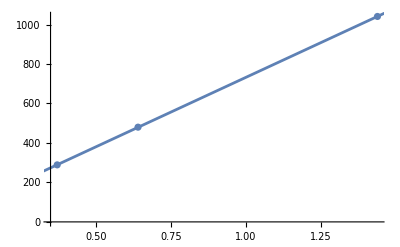

```mathematica
Show[ListPlot[lst],Plot[mod[x],{x,0,2}]]
```